```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Log[4/(0.13054 10^1)]
```

1.11978

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
```

```mathematica
FitError[func_,list_,p_]:=Module[{tab1,nbin},
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}];
If[p==Null,
tab1=Table[(list[[i,2]]-func[list[[i,1]]])^2,{i,1,Length[list]}],
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}]
];
nbin=Length[tab1];
√(Total[tab1]/(nbin-1))
]
```

```mathematica
iens=1;icoup=1;
```

```mathematica
path1=StringJoin[{"~/Code/Nchannel/Square/CODES/fort.",ToString[iens*1000+icoup]}]
```

~/Code/Nchannel/Square/CODES/fort.1001

```mathematica
yrange1={-7,4};
```

```mathematica
Data=DeleteCases[Import[path1,"Table"],{}];
```

```mathematica
iemax=Length[Data];iemin=1;
sigma=Table[{Data[[ie,2]],Data[[ie,10]]},{ie,iemin,iemax}];
lzclose=Table[{Data[[ie,2]], Log[Data[[ie,6]]]},{ie,iemin,iemax}];
alsqr=Table[{Data[[ie,2]],Data[[ie,5]]},{ie,iemin,iemax}];
albgsqr=Table[{Data[[ie,2]],Sin[Data[[ie,8]]]^2},{ie,iemin,iemax}];
phaseopi=Table[{Data[[ie,2]],Data[[ie,11]]},{ie,iemin,iemax}];
ltimedelay=Table[{Data[[ie,2]],Log[Data[[ie,12]]]},{ie,iemin,iemax}];
ascat = Table[{Data[[ie,2]],Data[[ie,4]]},{ie,iemin,iemax}];
abg=  Table[{Data[[ie,2]],Data[[ie,13]]},{ie,iemin,iemax}];
BSdet = Table[{Data[[ie,2]],Data[[ie,7]]},{ie,iemin,iemax}];
dtaude = Table[{Data[[ie,2]],Data[[ie,14]]},{ie,iemin,iemax}];
d2taude=Table[{Data[[ie,2]],Data[[ie,15]]},{ie,iemin,iemax}];
```

```mathematica
padding={{100,80},{80,0}};
imgsize={600,300};
yrange=All;
xrange={0,200};
aspctratio=Full;1/GoldenRatio;
pabg=ListPlot[abg,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a_bg/r_0"},LabelStyle->{16},PlotRange->{xrange,{-1000,1000}},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
palsqr=ListPlot[{alsqr,albgsqr},Joined->True,PlotStyle->{{Black},{Red,Dotted}},Frame->True,FrameLabel->{"E/(ℏ^2/2μ r_0^2)",TraditionalForm[Sin[δ]^2]},LabelStyle->{16},PlotRange->{xrange,yrange},GridLines->Automatic,ImageSize->imgsize,
ImagePadding->padding,
AspectRatio->aspctratio,FrameTicks->{Automatic,Automatic}];
psigma=ListPlot[sigma,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","σ/r_0^2"},LabelStyle->{16},PlotRange->{xrange,yrange},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
pstair=ListPlot[phaseopi,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","δ_0/π"},LabelStyle->{16},PlotRange->{xrange,All},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
plzc=ListPlot[lzclose,Joined->True,PlotStyle->{Red,Dashed},Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","ln(Z_C/r_0)"},LabelStyle->{16},PlotRange->{xrange,yrange1},GridLines->Automatic,
ImageSize->{600,250},
ImagePadding->{{100,80},{8,8}},
AspectRatio->aspctratio,ImageMargins->0,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
pltd=ListPlot[ltimedelay,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{(*"E/(ℏ^2/2μr_0^2)"*)None,TraditionalForm[Ln[(τ ℏ)/(2μ Subscript[r, 0]^2)]]},LabelStyle->Large,PlotRange->{xrange,yrange1},GridLines->Automatic,FrameTicks->{Automatic,Automatic},
ImageSize->{600,250},
ImagePadding->{{100,80},{8,8}},
AspectRatio->aspctratio,ImageMargins->0,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
pascat=ListPlot[ascat,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a/r_0"},LabelStyle->{16},PlotRange->{xrange,{-100,100}},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
```

```mathematica
pbsdet=ListPlot[BSdet,Joined->True,PlotStyle->Black,Frame->True,LabelStyle->{16},PlotRange->{xrange,{-10^-50,10^-50}},AspectRatio->50/1000,ImageSize->{600,50},PlotRangeClipping->False,ImagePadding->{{100,80},{0,20}},FrameTicks->{None,None},ImageMargins->0,Axes->False,Epilog->{Text[Style["(a)",Bold,22],{-30.,0}]}]
```

-Graphics-

```mathematica
AllResData=DeleteCases[Import["~/Code/Nchannel/Square/CODES/fort.800","Table"],{}];
ResData[iens_,icoup_]:=Select[Select[AllResData,(#[[2]]==iens)&],(#[[3]]==icoup)&]
Resonances = ResData[iens,icoup];
NumRes=Length[Resonances];

ResLines=Table[ssbg  (EE-ER+q Γ/2)^2/((EE-ER)^2+(Γ/2)^2)/.{ssbg->Resonances[[ires,9]],ER->Resonances[[ires,5]],Γ->Resonances[[ires,7]],q->Resonances[[ires,8]]},{ires,1,NumRes}];
resplots=Table[Plot[Evaluate[ResLines[[ires]]],{EE,Resonances[[ires,5]]-2Resonances[[ires,7]],Resonances[[ires,5]]+2Resonances[[ires,7]]},PlotStyle->{Blue,Dashed},PlotRange->All,ImagePadding->padding,ImageSize->imgsize,AspectRatio->Full],{ires,1,NumRes}];
```

```mathematica
resrootfunc[EE_]:=Product[EE-Resonances[[ires,5]],{ires,1,NumRes}]
```

```mathematica
pres=Plot[resrootfunc[EE],{EE,0,200},PlotStyle->Red,Frame->True,LabelStyle->{16},PlotRange->{xrange,{-10^-50,10^-50}},AspectRatio->50/1000,PlotRangeClipping->False,
ImageSize->{600,50},
ImagePadding->{{100,80},{0,20}},
FrameTicks->{None,None},ImageMargins->0,Axes->False,Epilog->{Text[Style["(a)",Bold,22],{-30.,0}]}]
```

-Graphics-

```mathematica
plines=Show[pres,pbsdet]
```

-Graphics-

```mathematica
widthdata=Table[{Resonances[[ires,5]],Resonances[[ires,7]]},{ires,1,NumRes}];
qdata=Table[{Resonances[[ires,5]],Resonances[[ires,8]]},{ires,1,NumRes}];
```

```mathematica
pwidth=ListPlot[widthdata,PlotStyle->Black,Frame->True,LabelStyle->Medium,FrameLabel->{"E","Γ/(ℏ^2/2μr_0^2)"}];
```

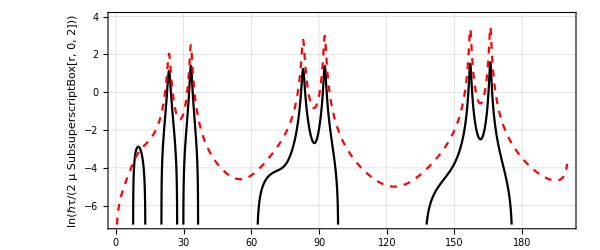

```mathematica
ptdlz=Show[{pltd,plzc},PlotRange->yrange1,FrameLabel->{{Text["ln(ℏτ/(2  μ SubsuperscriptBox[r, 0, 2]))" ],Text[Style["ln(Z_C/r_0)",Red]]},{None,None}},PlotRangeClipping->False,Epilog->{Text[Style["(b)",Bold,22],{-30,3.5}]}]
```

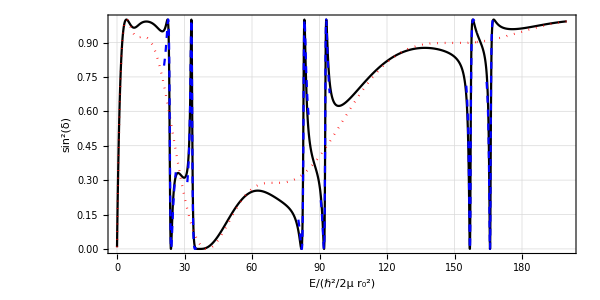

```mathematica
pfanolines = Show[{palsqr,resplots},PlotRange->{xrange,{0,1}},LabelStyle->Large,PlotRangeClipping->False,Epilog->{Text[Style["(c)",Bold,22],{-30,0.9}]}]
```

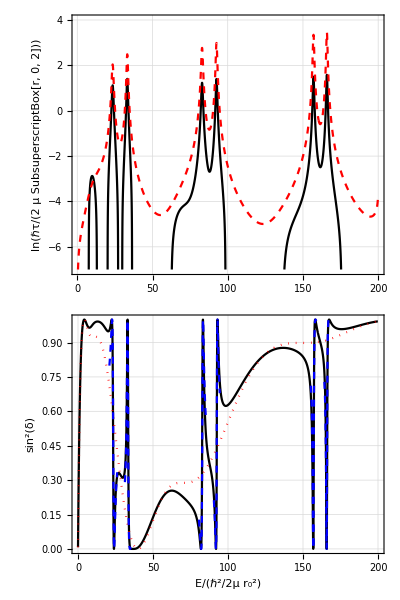

```mathematica
p1=Grid[{{plines},{ptdlz},{pfanolines}},Spacings->0]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pChris-Tridiag.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/pChris-Tridiag.pdf

Units of Z_C:

∫f gⅆr  ∝δ(k-k')~ 1/k~1/(√((2μ ϵ_0)/ℏ^2))~1/(√((2μ)/ℏ^2 ℏ^2/(2μ r_0^2)))~r_0

Okay,

Γ^(i)=(4ℏ)/(τ(E^(i))) → τ(E^(i))=(4ℏ)/Γ^(i)

We found numerically that:

Z_C=2/(Γ^(i)/√(E^(i)))

The right hand side should have units of 1/(√ϵ_0)=√((2μ r_0^2)/ℏ^2)=√(2μ)r_0/ℏ while the left hand side should have units of r_0.  Therefore I propose the relation is:

Z_C=(2ℏ)/(√(2μ)Γ^(i)/√(E^(i)))

Z_C=(4ℏ √(E^(i)))/(2 √(2μ)Γ^(i))=(τ(E^(i))√(E^(i)))/(2 √(2μ))

so that now the right hand side also has units of length.

(τ(E)√E)/(2 √(2μ))

```mathematica
B=Interpolation[BSdet]
```

InterpolatingFunction[{{0.1, 199.88}}, <>]

```mathematica
FindRoot[B[x]==0,{x,20}]
```

{x→23.1144}

```mathematica
FindRoot[B[x]==0,{x,31}]
```

{x→32.8931}

```mathematica
FindRoot[B[x]==0,{x,81}]
```

{x→82.8363}

```mathematica
FindRoot[B[x]==0,{x,91}]
```

{x→92.3623}

```mathematica
FindRoot[B[x]==0,{x,150}]
```

{x→157.004}

```mathematica
FindRoot[B[x]==0,{x,170}]
```

{x→165.827}

```mathematica
wfns=DeleteCases[Import["~/Code/Nchannel/Square/CODES/fort.100","Table"],{}];
psi=Table[Table[{wfns[[i,1]],wfns[[i,j+1]]},{i,1,npsi}],{j,1,3}];
npsi=Length[wfns];ListPlot[{Legended[psi[[1]],Placed["i=1 closed",{.8,.95}]],Legended[psi[[2]],Placed["i=2 closed",{.8,.85}]],Legended[psi[[3]],Placed["i=3 open",{.8,.75}]]},Joined->True,Frame->True,LabelStyle->Large,GridLines->Automatic,PlotStyle->{{Red,Dashed},{Blue,Dotted},{Black}},FrameLabel->{"r/r_0","ψ_i(r)"},ImageSize->{600,400}]
```

Import::nffil: File not found during Import.

-Graphics-

126

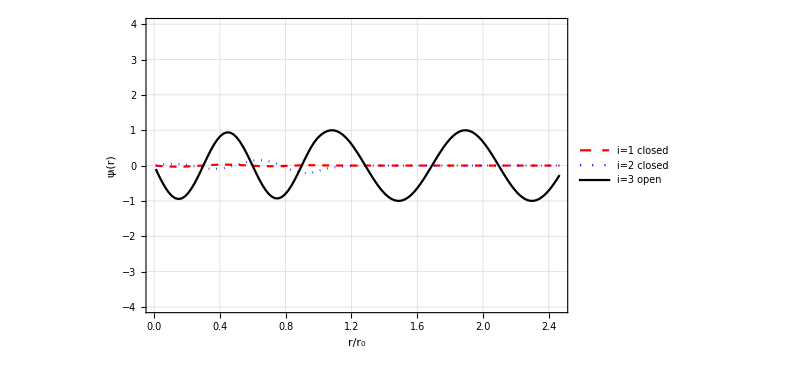

```mathematica
wfns2=DeleteCases[Import["~/Code/Nchannel/Square/CODES/fort.100","Table"],{}];
npsi2=Length[wfns2];
psi2=Table[Table[{wfns2[[i,1]],wfns2[[i,j+1]]},{i,1,npsi2}],{j,1,3}];
ListPlot[{Legended[psi2[[1]],Placed["i=1 closed",{.8,.95}]],Legended[psi2[[2]],Placed["i=2 closed",{.8,.85}]],Legended[psi2[[3]],Placed["i=3 open",{.8,.75}]]},Joined->True,Frame->True,LabelStyle->Large,GridLines->Automatic,PlotRange->{-4,4},PlotStyle->{{Red,Dashed},{Blue,Dotted},{Black}},FrameLabel->{"r/r_0","ψ_i(r)"},ImageSize->{600,400}]
```